{{a[n]→1/2 (2+n+n^2)}}

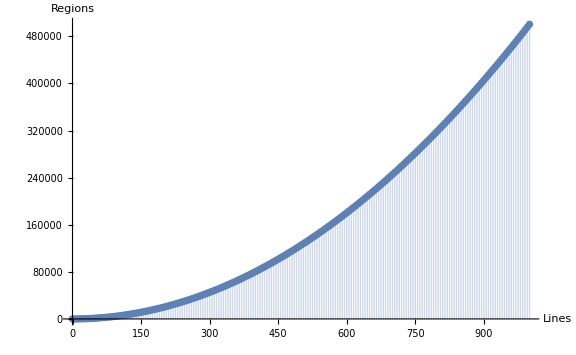

Result {lines, regions}: 
{{0,1},{5,16},{10,56},{15,121},{20,211},{25,326},{30,466},{35,631},{40,821},{45,1036},{50,1276},{55,1541},{60,1831},{65,2146},{70,2486},{75,2851},{80,3241},{85,3656},{90,4096},{95,4561},{100,5051},{105,5566},{110,6106},{115,6671},{120,7261},{125,7876},{130,8516},{135,9181},{140,9871},{145,10586},{150,11326},{155,12091},{160,12881},{165,13696},{170,14536},{175,15401},{180,16291},{185,17206},{190,18146},{195,19111},{200,20101},{205,21116},{210,22156},{215,23221},{220,24311},{225,25426},{230,26566},{235,27731},{240,28921},{245,30136},{250,31376},{255,32641},{260,33931},{265,35246},{270,36586},{275,37951},{280,39341},{285,40756},{290,42196},{295,43661},{300,45151},{305,46666},{310,48206},{315,49771},{320,51361},{325,52976},{330,54616},{335,56281},{340,57971},{345,59686},{350,61426},{355,63191},{360,64981},{365,66796},{370,68636},{375,70501},{380,72391},{385,74306},{390,76246},{395,78211},{400,80201},{405,82216},{410,84256},{415,86321},{420,88411},{425,90526},{430,92666},{435,94831},{440,97021},{445,99236},{450,101476},{455,103741},{460,106031},{465,108346},{470,110686},{475,113051},{480,115441},{485,117856},{490,120296},{495,122761},{500,125251},{505,127766},{510,130306},{515,132871},{520,135461},{525,138076},{530,140716},{535,143381},{540,146071},{545,148786},{550,151526},{555,154291},{560,157081},{565,159896},{570,162736},{575,165601},{580,168491},{585,171406},{590,174346},{595,177311},{600,180301},{605,183316},{610,186356},{615,189421},{620,192511},{625,195626},{630,198766},{635,201931},{640,205121},{645,208336},{650,211576},{655,214841},{660,218131},{665,221446},{670,224786},{675,228151},{680,231541},{685,234956},{690,238396},{695,241861},{700,245351},{705,248866},{710,252406},{715,255971},{720,259561},{725,263176},{730,266816},{735,270481},{740,274171},{745,277886},{750,281626},{755,285391},{760,289181},{765,292996},{770,296836},{775,300701},{780,304591},{785,308506},{790,312446},{795,316411},{800,320401},{805,324416},{810,328456},{815,332521},{820,336611},{825,340726},{830,344866},{835,349031},{840,353221},{845,357436},{850,361676},{855,365941},{860,370231},{865,374546},{870,378886},{875,383251},{880,387641},{885,392056},{890,396496},{895,400961},{900,405451},{905,409966},{910,414506},{915,419071},{920,423661},{925,428276},{930,432916},{935,437581},{940,442271},{945,446986},{950,451726},{955,456491},{960,461281},{965,466096},{970,470936},{975,475801},{980,480691},{985,485606},{990,490546},{995,495511},{1000,500501}}

```mathematica
(*Clear everything*)
Clear["`*"];
(*Initial condition: 0 line, 1 plane; 1 line, 2 half-planes (regions) *)
iv1=a[0]==1;
iv2=a[1]==2;
(*Since there is no parallel nor *** line, one new line will cross n lines, cross n regions plus the final empty halfplane, divides it into 2 halfplanes *)
rr=a[n+1]==a[n]+n+1;
(*Solve it by Mathematica (not fun) *)
sol=RSolve[{rr,iv1,iv2},a[n],n] // Simplify
a[n_]=a[n]/.sol[[1]];
(*Exporting and ploting*)
(*Adopted partly from: https://mathematica.stackexchange.com/questions/1854/adding-labels-to-points-in-listplot*)
data = Table[{n,a[n]},{n,0,1000,5}];
dataPlot=ListPlot[data,AxesLabel->{Lines,Regions},Filling->Axis];
Show[dataPlot,
Graphics[{Blue}]
]

Print["Result {lines, regions}: \n",data];
```